# Thesis Project: Cement Hydrates C-H-S

## K-Points Analysis

### Working directory

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/";
SetDirectory[wrkdir]
```

/home/qbit/Documents/git-repositories/bachelor-thesis

### The k-point grid

```mathematica
bulk = Import["./dftb/eos/POSCAR-init", "Table"];
```

```mathematica
lattbulk = bulk[[2, 1]] bulk[[3;;5]]
```

{{13.5354,0.18446,0.00755401},{-16.2629,24.8887,-0.00875423},{0.543338,-0.483321,23.4374}}

```mathematica
{a, b, c} = lattbulk;
```

```mathematica
Δk = Table[0.07-0.005 i, {i, 0, 10}];
```

```mathematica
Δk//Map[{#, Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&, #]&//TableForm
```

0.07 | 1 | 1 | 1
0.065 | 1 | 1 | 1
0.06 | 1 | 1 | 1
0.055 | 2 | 1 | 1
0.05 | 2 | 1 | 1
0.045 | 2 | 1 | 1
0.04 | 2 | 1 | 1
0.035 | 2 | 1 | 1
0.03 | 3 | 1 | 1
0.025 | 3 | 2 | 2
0.02 | 4 | 2 | 2

We will run the xkp.sh script for k-points densities 0.06, 0.04, and 0.03

### Convergency of k-points

```mathematica
data = Import["./dftb/kp.dat"]
```

{{1,-4660.48,43},{2,-4660.51,58},{3,-4660.51,37}}

```mathematica
kpdat =data[[All,{1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

#### Get the x and y data:

```mathematica
kpY=kpdat[[All,2]]
kpX={0.06,0.04,0.03}
```

{-6.75432,-6.75437,-6.75436}

{0.06,0.04,0.03}

#### Plot the data:

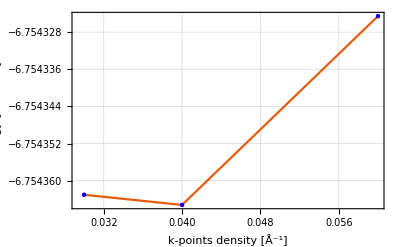

```mathematica
ListPlot[
Transpose[{kpX,kpY}],
PlotTheme->"Scientific",
GridLines->Automatic,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

#### Let’s analyse the convergency of these data using the 1 meV/atom criteria

```mathematica
energyMin=kpdat[[1,2]]+10^-3/2;
energyMax=kpdat[[1,2]]-10^-3/2;
```

```mathematica
kPlot=ListPlot[
Transpose[{kpX,kpY}],
PlotRange->{kpdat[[1,2]]+10^-3, kpdat[[1,2]]-10^-3},
PlotTheme->"Scientific",
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400];
```

```mathematica
energyWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{0.02,energyMin},{0.07,energyMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{0.02,energyMin},{0.07,energyMin}}]},{Dashed,Black,Line[{{0.02,energyMax},{0.07,energyMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{0.05,energyMin},{0.05,energyMax}}]},Text[Style["1 meV",FontSize->12,Black],{0.053,0.0001+Mean[{energyMin,energyMax}]}]}];
```

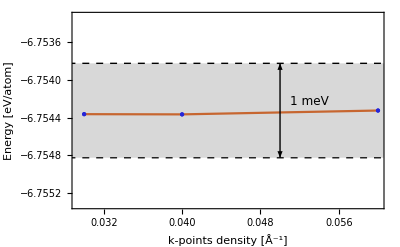

```mathematica
Show[kPlot, energyWindow]
```

From this result, we use from now on the k-point grid 1x1x1

## Cut-off Energy Analysis

### ENCUT

```mathematica
datacem = Import["./dftb/ecut.dat"];
```

```mathematica
dataecut=datacem[[All,{1,2}]]//Map[#/{1,690}&];
```

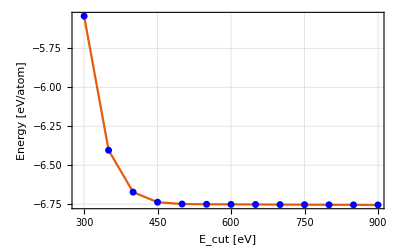

```mathematica
dataecut//ListPlot[#,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"E_cut [eV]","Energy [eV/atom]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

We  use meV precision because magnetic properties are really tiny. So we need this precision to describe these properties.

```mathematica
encutMin=dataecut[[13,2]];
encutMax=dataecut[[13,2]]+10^-3;
```

```mathematica
encutPlot =dataecut//ListPlot[#,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"E_cut [eV]","Energy [meV/atom]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,(*{{350,950},{dataecut[[13,2]], dataecut[[2,2]]}},*)
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&;
```

```mathematica
encutWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{200,encutMin},{950,encutMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{200,encutMin},{950,encutMin}}]},{Dashed,Black,Line[{{200,encutMax},{950,encutMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{750,encutMin},{750,encutMax}}]},Text[Style["1 meV",FontSize->12,Black],{800,Mean[{encutMin,encutMax}]}]}];
```

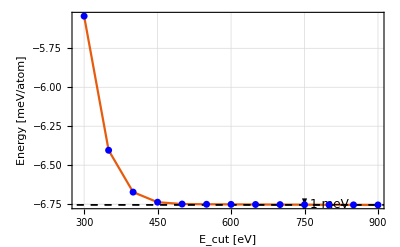

```mathematica
Show[encutPlot,encutWindow]
```

We  use 800 meV for  CSH analysis from now on.

## Density of States

```mathematica
pdosData=Import["./cluster-files/DOSCAR-cem1.sto", "Table"];
```

```mathematica
Dimensions[pdosData]
```

{2074387}

```mathematica
dos = pdosData[[7;;7+3000]][[All, {1, 2}]];
```

```mathematica
ef = pdosData[[6, 4]]
```

3.069

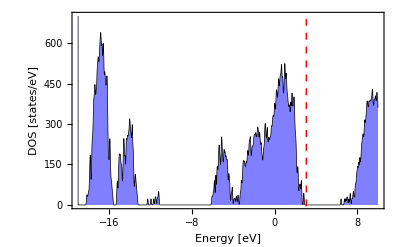

```mathematica
ListPlot[dos, 
PlotTheme->"Scientific",
Joined->True,
Axes->False,
Frame->True,
FrameLabel->
{"Energy [eV]", 
"DOS [states/eV]"},
GridLines->{{ef}, None},
GridLinesStyle-> 
Directive[Red, Dashed,
AbsoluteThickness[1]],
BaseStyle->
{FontFamily->"Helvetica",
FontSize->15},
Filling->Axis,
FillingStyle->
Directive[Opacity[0.5], Blue],
PlotStyle-> 
{AbsoluteThickness[0.5], Black},
ImageSize->400,
PlotRange->{All, {0, 700}}]
```

### Partial Density of States PDOS

Let us define the number of atoms of each element.

```mathematica
atomsCa=99;
atomsSi=60;
atomsO=323;
atomsH=208;
```

## Benchmark

```mathematica
benchRes=Import["./cluster-files/results.dat"]
```

{{1,552.512},{2,308.492},{3,235.218},{5,186.864},{7,213.865},{9,187.9},{11,228.094}}

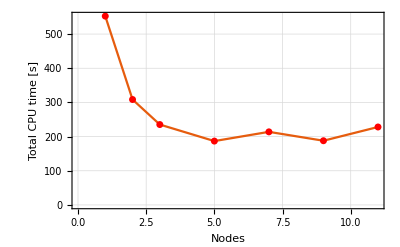

```mathematica
ListPlot[benchRes,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Nodes","Total CPU time [s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[benchRes]}]
```

```mathematica
benchRes[[All,1]];
```

```mathematica
scaleTCPU=benchRes//Map[#/{1,benchRes[[1,2]]}&];
```

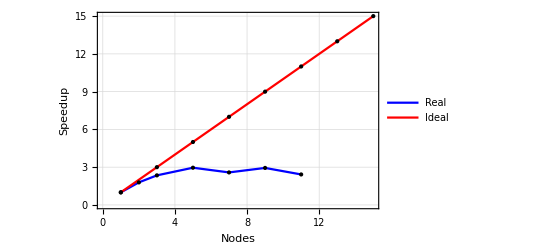

```mathematica
ListPlot[{
Transpose[{scaleTCPU[[All,1]],1/scaleTCPU[[All,2]]}],
Transpose[{Range[1,15,2], Range[1,15,2]}]},
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Nodes","Speedup"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
PlotStyle->{Blue, Red},
PlotLegends->Placed[{"Real", "Ideal"} ,After],
Mesh->All,
MeshStyle->
{Directive[PointSize[Medium], Black]}]
```

## MLFF Results Analysis

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/";
SetDirectory[wrkdir]
```

/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files

### Optimal Volume

```mathematica
optVolume=Import["volume.dat"][[All,1]];
```

```mathematica
timeData=2/10^3 Range[0,50000-1]; (*In μs*)
```

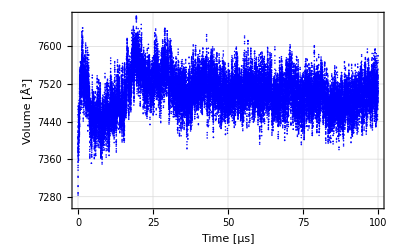

```mathematica
ListPlot[
Transpose[{timeData,optVolume}],
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Time [μs]","Volume [Å^3]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Blue,
ImageSize->400]
```

### Total Energy

```mathematica
totEnergy=Import["entot.dat"][[All,1]];
```

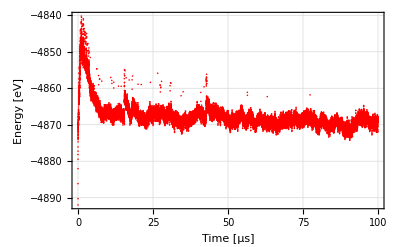

```mathematica
ListPlot[
Transpose[{timeData,totEnergy}],
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Time [μs]","Energy [eV]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Red,
ImageSize->400]
```

### BEEF & ERR

Get the beef and err data from the ML_LOGFILE from the training process

```mathematica
Run["grep 'BEEF' ML_LOGFILE | tail -n +15 | awk '{print $2\"   \"$4}' > beef.dat"];
```

```mathematica
beefData = Import["beef.dat"];
```

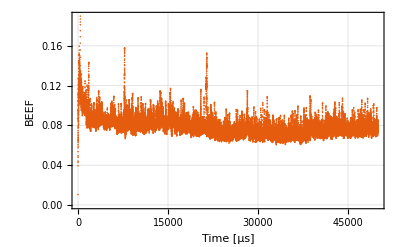

```mathematica
beefData//ListPlot[#,PlotRange->All,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
Joined->False,
FrameLabel->{"Time [μs]","BEEF"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]&
```

### RCUT 1

```mathematica
rcut1Error=Import["ml_error/rcut1/training_error.dat"];
```

```mathematica
(*Extract numerical data*)
rcut1Data=rcut1Error[[2;;]];
```

```mathematica
(*Extract rcut values and each column*)
rcutValues1=rcut1Data[[All,1]];
energyValues1=rcut1Data[[All,2]];
forceValues1=rcut1Data[[All,3]];
stressValues1=rcut1Data[[All,4]];
```

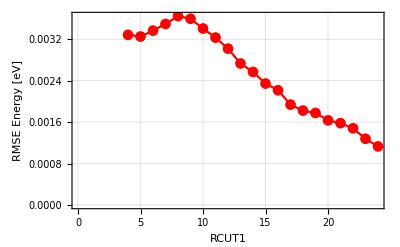

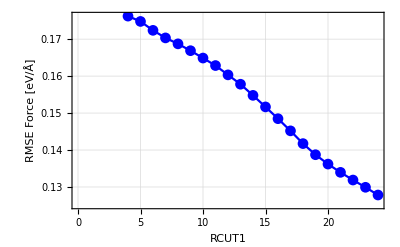

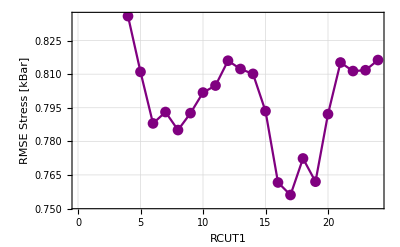

```mathematica
energyPlot1=
ListLinePlot[
Transpose[{rcutValues1,energyValues1}],
PlotMarkers->Automatic,
PlotStyle->Red,
Frame->True,
FrameLabel->{"RCUT1","RMSE Energy [eV]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

forcePlot1=
ListLinePlot[Transpose[{rcutValues1,forceValues1}],
PlotMarkers->Automatic,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"RCUT1","RMSE Force [eV/Å]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific"
];

stressPlot1=
ListLinePlot[Transpose[{rcutValues1,stressValues1}],
PlotMarkers->Automatic,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"RCUT1","RMSE Stress [kBar]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific"
];

(*Show all plots separately*)
energyPlot1
forcePlot1
stressPlot1
```

### RCUT 2

```mathematica
rcut2Error=Import["ml_error/rcut2/training_error.dat"];
```

```mathematica
(*Extract numerical data*)
rcut2Data=rcut2Error[[2;;]];
```

```mathematica
(*Extract rcut values and each column*)
rcutValues2=rcut2Data[[All,1]];
energyValues2=rcut2Data[[All,2]];
forceValues2=rcut2Data[[All,3]];
stressValues2=rcut2Data[[All,4]];
```

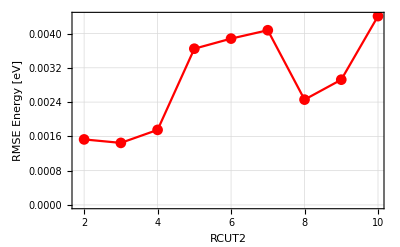

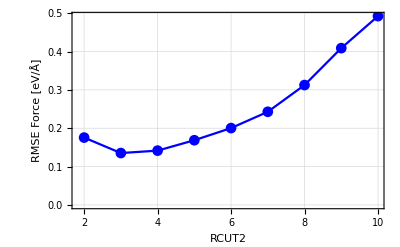

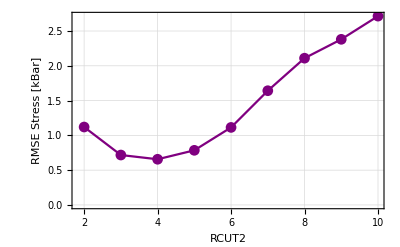

```mathematica
energyPlot2=
ListLinePlot[
Transpose[{rcutValues2,energyValues2}],
PlotMarkers->Automatic,
PlotStyle->Red,
Frame->True,
FrameLabel->{"RCUT2","RMSE Energy [eV]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

forcePlot2=
ListLinePlot[Transpose[{rcutValues2,forceValues2}],
PlotMarkers->Automatic,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"RCUT2","RMSE Force [eV/Å]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

stressPlot2=
ListLinePlot[Transpose[{rcutValues2,stressValues2}],
PlotMarkers->Automatic,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"RCUT2","RMSE Stress [kBar]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

(*Show all plots separately*)
energyPlot2
forcePlot2
stressPlot2
```

## RMSE ENERGY, FORCE & STRESS

### TOTAL ENERGY

```mathematica
dtfTOTEN=Import["ml_error/dft_data/dft_toten.dat"];
```

```mathematica
mlTOTEN=Import["ml_error/ml_data/ml_toten.dat"];
```

```mathematica
rmseTOTEN= (mlTOTEN[[All,2]] - dtfTOTEN[[All,2]])/690;
```

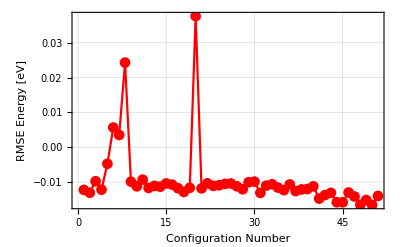

```mathematica
ListLinePlot[rmseTOTEN,
PlotRange->All,
PlotMarkers->Automatic,
PlotTheme->"Scientific" ,
GridLines->Automatic,
PlotStyle->Red,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Energy [eV]"}]
```

### RMSE FORCE

```mathematica
rmseForce=Import["ml_error/ml_rmse_force.dat"];
```

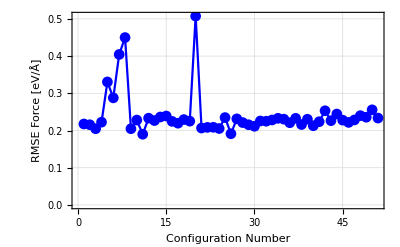

```mathematica
ListLinePlot[rmseForce[[2;;]],
PlotRange->All,
PlotMarkers->Automatic,
PlotTheme->"Scientific" ,
GridLines->Automatic,
PlotStyle->Blue,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Force [eV/Å]"}]
```

### RMSE STRESS

```mathematica
rmseStress=Import["ml_error/rmse_stress.dat"][[2;;,All]];
```

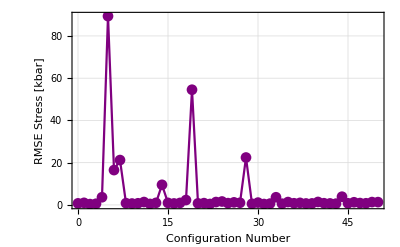

```mathematica
ListLinePlot[rmseStress,
PlotRange->All,
PlotMarkers->Automatic,
PlotTheme->"Scientific" ,
GridLines->Automatic,
PlotStyle->Purple,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Stress [kbar]"}]
```